```mathematica
Manipulate[Plot[Sin[a x],{x,0,2 Pi}],{a,1,10}]
```

```mathematica
network[v_,e_]:=Graph[RandomInteger[{1,v},{e,2}]/.
{x_Integer,y_Integer}:>RandomChoice[{DirectedEdge[x,y],UndirectedEdge[x,y]}]]

SeedRandom[131];g=network[20,60]
```

-Graphics-

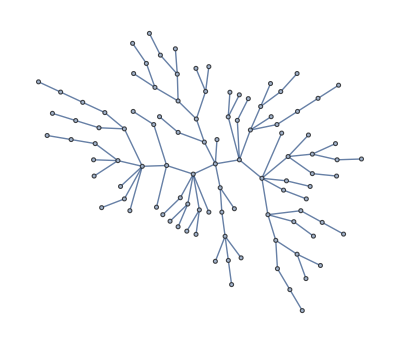

```mathematica
TreeGraph[RandomInteger[#]<->#+1&/@Range[0,100],GraphLayout->"RadialDrawing"]
```

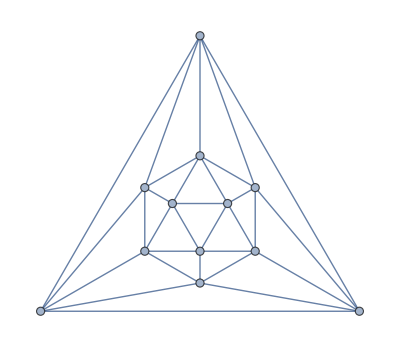

```mathematica
GraphData["IcosahedralGraph"]
```

```mathematica
g=ExampleData[{"NetworkGraph","MetabolicNetworkSaccharomycesCerevisiae"}];

<<IGraphM`

group=IGBlissAutomorphismGroup[g];
```

$Failed

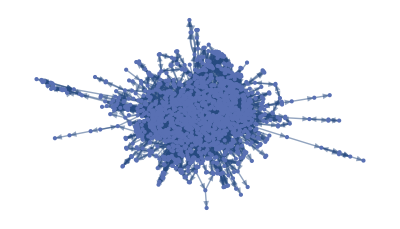
IGBlissAutomorphismGroup[PermutationCycles[-Graphics-]]

{Cycles[{{200,249},{201,250}}],Cycles[{{480,484},{481,485},{1041,1042},{1113,1449}}],Cycles[{{536,539},{537,540},{610,615},{611,616},{1262,1268},{1263,1269},{1264,1270}}],Cycles[{{541,557},{617,642},{949,1271},{952,1272}}],Cycles[{{1315,1438}}],Cycles[{{1497,1498}}]}

```mathematica
PermutationCycles/@group

{Cycles[{{200,249},{201,250}}],Cycles[{{480,484},{481,485},{1041,1042},{1113,1449}}],Cycles[{{536,539},{537,540},{610,615},{611,616},{1262,1268},{1263,1269},{1264,1270}}],Cycles[{{541,557},{617,642},{949,1271},{952,1272}}],Cycles[{{1315,1438}}],Cycles[{{1497,1498}}]}
```

```mathematica
vi=Flatten/@First/@PermutationCycles/@group
```

IGBlissAutomorphismGroup[Flatten[-Graphics-]]

```mathematica
Table[vv=VertexList[g][[ind]];
HighlightGraph[NeighborhoodGraph[g,vv,2],vv],{ind,vi}]
```

Table[vv=VertexList[g]⟦ind⟧;HighlightGraph[NeighborhoodGraph[g,vv,2],vv],{ind,IGBlissAutomorphismGroup[Flatten[-Graphics-]]}]

```mathematica
GraphAutomorphismGroup[ExampleData["NetworkGraph"]]
PermutationGroup[{Cycles[{{32,33}}],Cycles[{{31,32}}],Cycles[{{30,31}}],Cycles[{{29,30}}],Cycles[{{16,18}}],Cycles[{{5,11},{6,7}}]}]
```

PermutationGroup[{Cycles[{{32,33}}],Cycles[{{31,32}}],Cycles[{{30,31}}],Cycles[{{29,30}}],Cycles[{{16,18}}],Cycles[{{5,11},{6,7}}]}]

```mathematica
GraphAutomorphismGroup[ExampleData[{"NetworkGraph","CoauthorshipsInNetworkScience"}]]
```